# Сигнальные созвездия

## QAM

Без шума

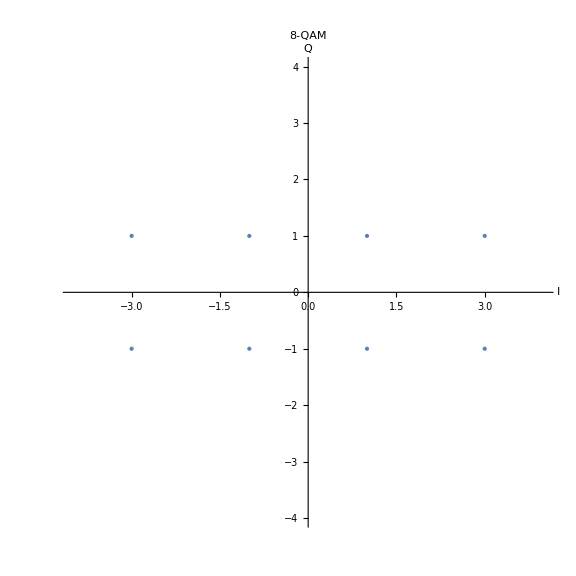

C:\Modulation\Constellation diagram\qam8n0a0.jpg

```mathematica
qam8n0a0=ListPlot[Flatten[Table[{i,q},{i,-3,3,2},{q,-1,1,2}],1],PlotStyle->PointSize[Large],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["8-QAM"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam8n0a0.jpg",qam8n0a0]
```

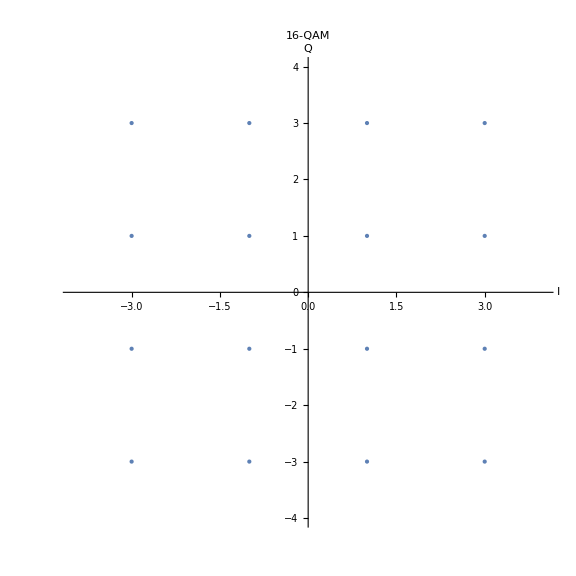

C:\Modulation\Constellation diagram\qam16n0a0.jpg

```mathematica
qam16n0a0=ListPlot[Flatten[Table[{i,q},{i,-3,3,2},{q,-3,3,2}],1],PlotStyle->PointSize[Large],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-QAM"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam16n0a0.jpg",qam16n0a0]
```

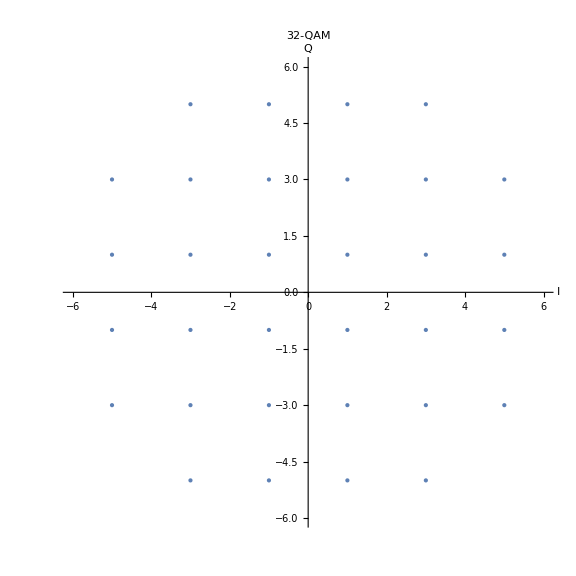

C:\Modulation\Constellation diagram\qam32n0a0.jpg

```mathematica
qam32n0a0=ListPlot[Flatten[{Flatten[Table[{i,q},{i,-5,5,2},{q,-3,3,2}],1],Flatten[Table[{i,q},{i,-3,3,2},{q,-5,5,10}],1]},1],PlotStyle->PointSize[Large],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-QAM"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam32n0a0.jpg",qam32n0a0]
```

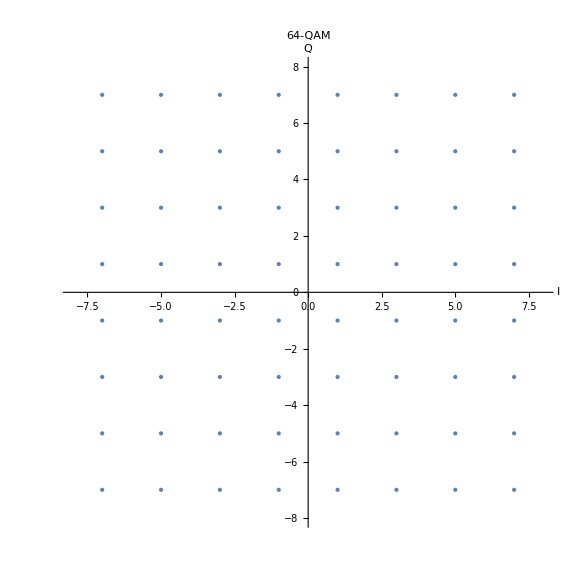

C:\Modulation\Constellation diagram\qam64n0a0.jpg

```mathematica
qam64n0a0=ListPlot[Flatten[Table[{i,q},{i,-7,7,2},{q,-7,7,2}],1],PlotStyle->PointSize[Large],PlotRange->{{-8,8},{-8,8}},AspectRatio->1,PlotLabel->Style[Framed["64-QAM"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam64n0a0.jpg",qam64n0a0]
```

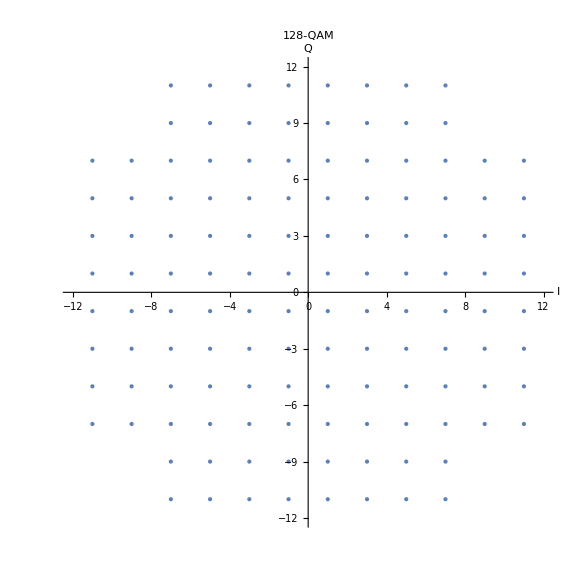

C:\Modulation\Constellation diagram\qam128n0a0.jpg

```mathematica
qam128n0a0=ListPlot[Flatten[{Flatten[Table[{i,q},{i,-11,11,2},{q,-7,7,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,-11,-9,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,9,11,2}],1]},1],PlotStyle->PointSize[Large],PlotRange->{{-12,12},{-12,12}},AspectRatio->1,PlotLabel->Style[Framed["128-QAM"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam128n0a0.jpg",qam128n0a0]
```

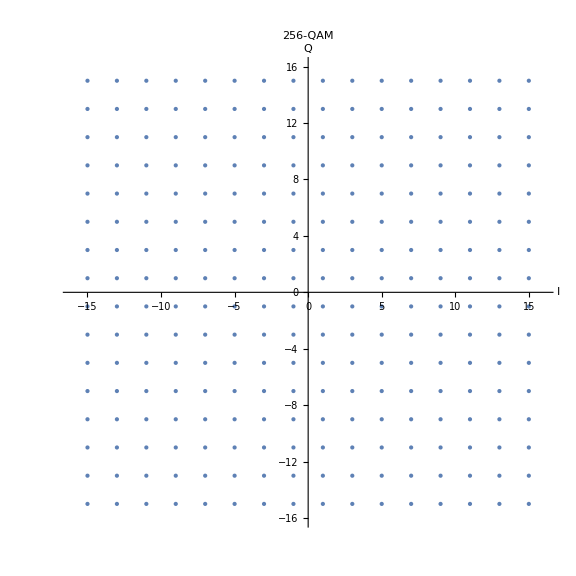

C:\Modulation\Constellation diagram\qam256n0a0.jpg

```mathematica
qam256n0a0=ListPlot[Flatten[Table[{i,q},{i,-15,15,2},{q,-15,15,2}],1],PlotStyle->PointSize[Large],PlotRange->{{-16,16},{-16,16}},AspectRatio->1,PlotLabel->Style[Framed["256-QAM"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam256n0a0.jpg",qam256n0a0]
```

С шумом Δ∈{-0.1A, 0.1A}

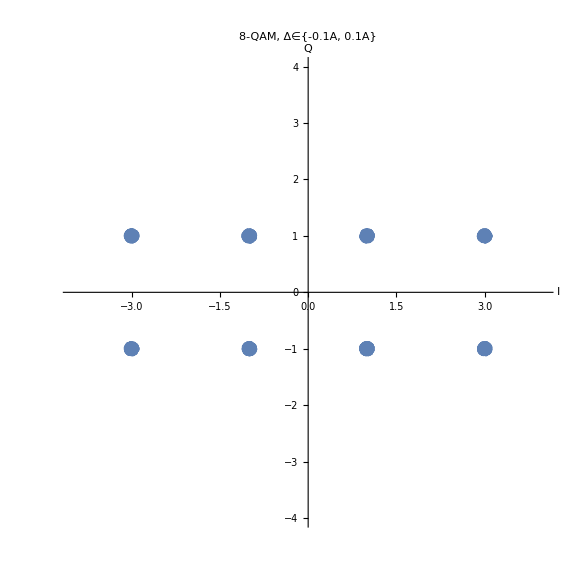

C:\Modulation\Constellation diagram\qam8n1a0.jpg

```mathematica
qam8n1a0=ListPlot[Transpose[Module[{n=8000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-1,1,2}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["8-QAM, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam8n1a0.jpg",qam8n1a0]
```

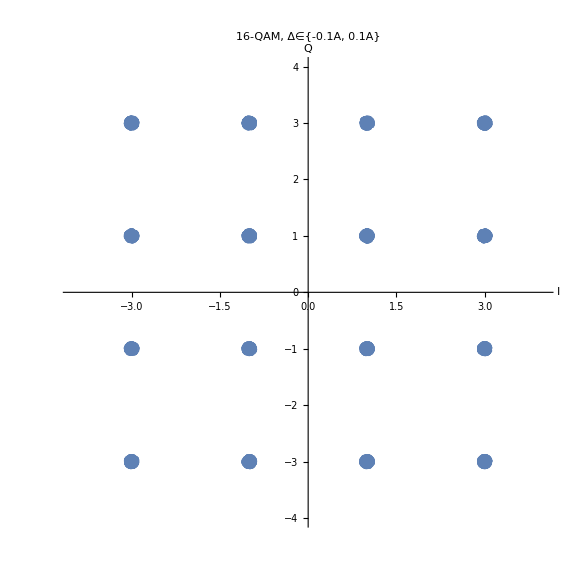

C:\Modulation\Constellation diagram\qam16n1a0.jpg

```mathematica
qam16n1a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-3,3,2}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-QAM, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam16n1a0.jpg",qam16n1a0]
```

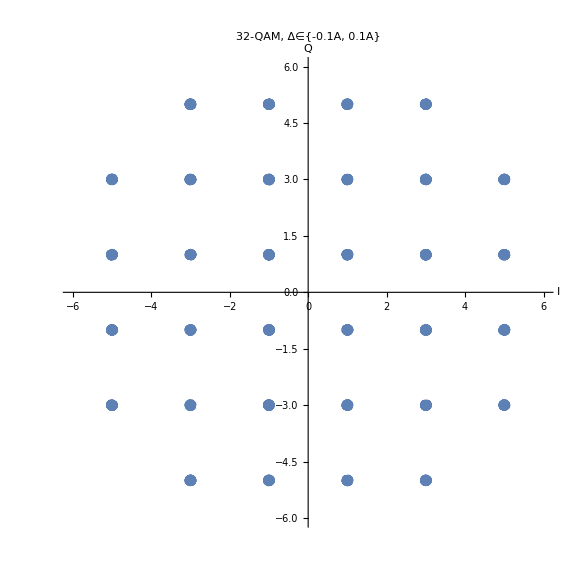

C:\Modulation\Constellation diagram\qam32n1a0.jpg

```mathematica
qam32n1a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-5,5,2},{q,-3,3,2}],1],Flatten[Table[{i,q},{i,-3,3,2},{q,-5,5,10}],1]},1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-QAM, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam32n1a0.jpg",qam32n1a0]
```

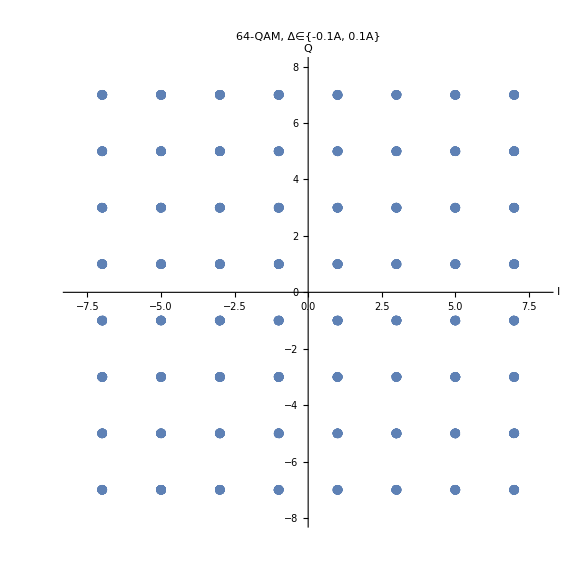

C:\Modulation\Constellation diagram\qam64n1a0.jpg

```mathematica
qam64n1a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-7,7,2},{q,-7,7,2}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-8,8},{-8,8}},AspectRatio->1,PlotLabel->Style[Framed["64-QAM, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam64n1a0.jpg",qam64n1a0]
```

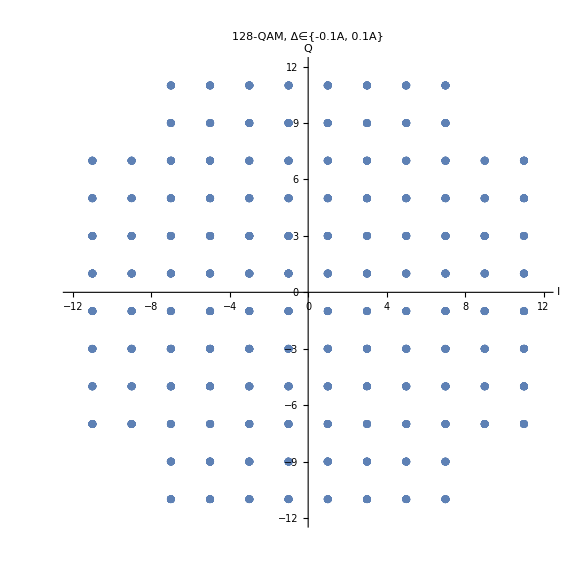

C:\Modulation\Constellation diagram\qam128n1a0.jpg

```mathematica
qam128n1a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-11,11,2},{q,-7,7,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,-11,-9,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,9,11,2}],1]},1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-12,12},{-12,12}},AspectRatio->1,PlotLabel->Style[Framed["128-QAM, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam128n1a0.jpg",qam128n1a0]
```

```mathematica
qam256n1a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-15,15,2},{q,-15,15,2}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-16,16},{-16,16}},AspectRatio->1,PlotLabel->Style[Framed["256-QAM, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam256n1a0.jpg",qam256n1a0]
```

-Graphics-

C:\Modulation\Constellation diagram\qam256n1a0.jpg

С шумом Δ∈{-0.25A, 0.25A}

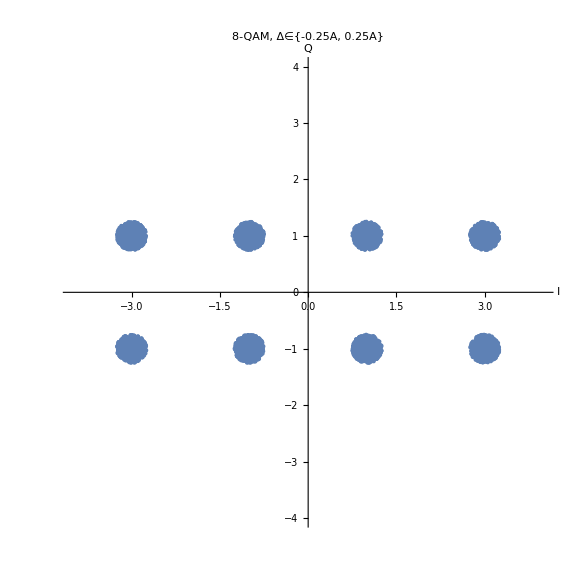

C:\Modulation\Constellation diagram\qam8n2a0.jpg

```mathematica
qam8n2a0=ListPlot[Transpose[Module[{n=8000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-1,1,2}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["8-QAM, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam8n2a0.jpg",qam8n2a0]
```

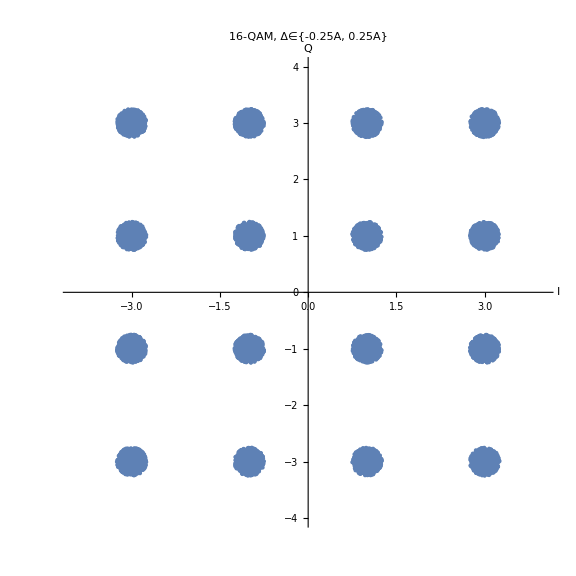

C:\Modulation\Constellation diagram\qam16n2a0.jpg

```mathematica
qam16n2a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-3,3,2}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-QAM, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam16n2a0.jpg",qam16n2a0]
```

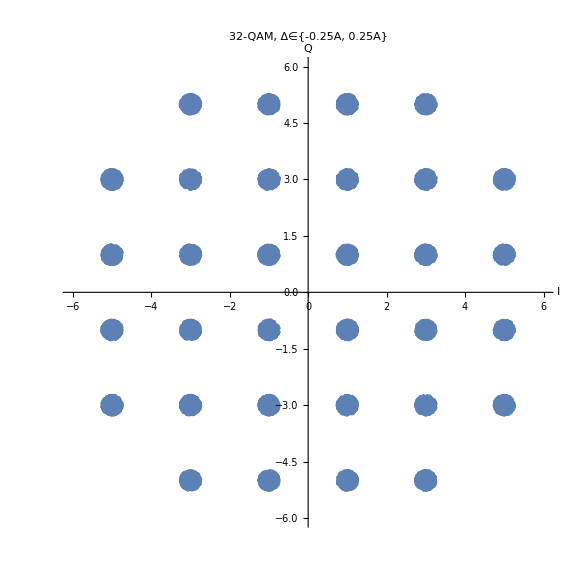

C:\Modulation\Constellation diagram\qam32n2a0.jpg

```mathematica
qam32n2a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-5,5,2},{q,-3,3,2}],1],Flatten[Table[{i,q},{i,-3,3,2},{q,-5,5,10}],1]},1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-QAM, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam32n2a0.jpg",qam32n2a0]
```

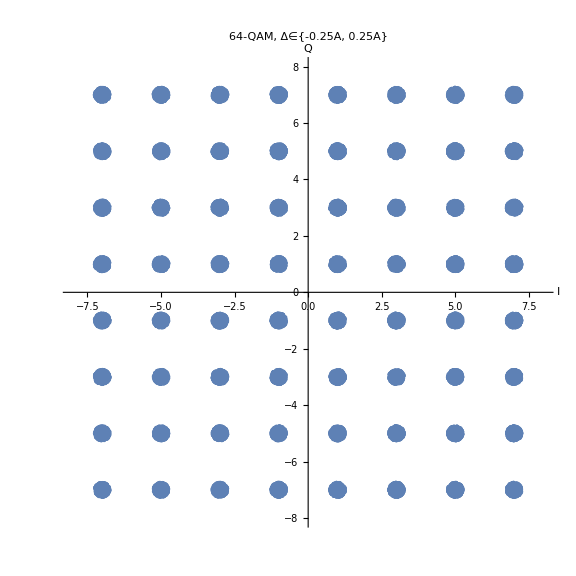

C:\Modulation\Constellation diagram\qam64n2a0.jpg

```mathematica
qam64n2a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-7,7,2},{q,-7,7,2}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-8,8},{-8,8}},AspectRatio->1,PlotLabel->Style[Framed["64-QAM, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam64n2a0.jpg",qam64n2a0]
```

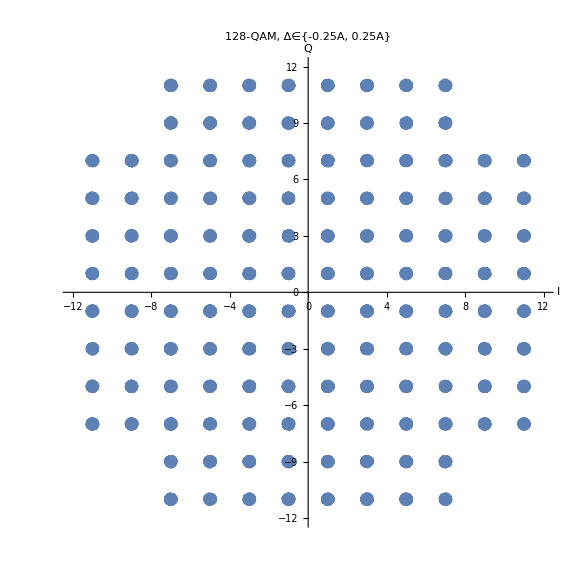

C:\Modulation\Constellation diagram\qam128n2a0.jpg

```mathematica
qam128n2a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-11,11,2},{q,-7,7,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,-11,-9,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,9,11,2}],1]},1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-12,12},{-12,12}},AspectRatio->1,PlotLabel->Style[Framed["128-QAM, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam128n2a0.jpg",qam128n2a0]
```

```mathematica
qam256n2a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-15,15,2},{q,-15,15,2}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-16,16},{-16,16}},AspectRatio->1,PlotLabel->Style[Framed["256-QAM, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam256n2a0.jpg",qam256n2a0]
```

-Graphics-

C:\Modulation\Constellation diagram\qam256n2a0.jpg

С шумом Δ∈{-0.5A, 0.5A}

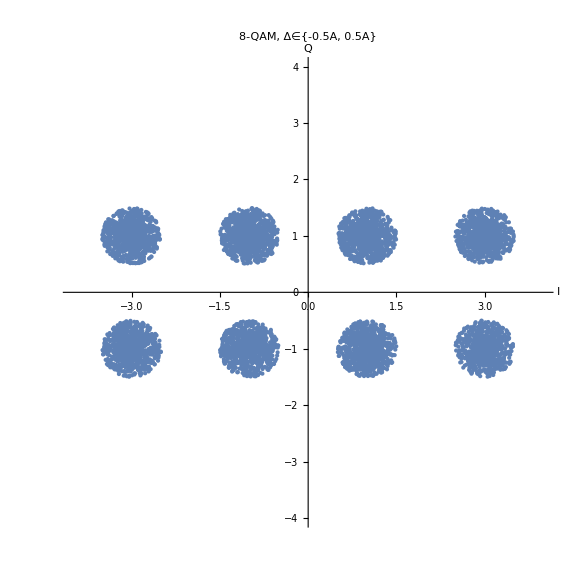

C:\Modulation\Constellation diagram\qam8n3a0.jpg

```mathematica
qam8n3a0=ListPlot[Transpose[Module[{n=8000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-1,1,2}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["8-QAM, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam8n3a0.jpg",qam8n3a0]
```

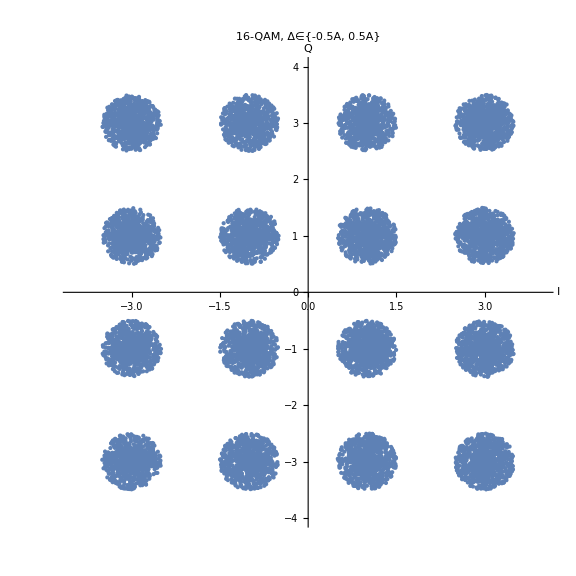

C:\Modulation\Constellation diagram\qam16n3a0.jpg

```mathematica
qam16n3a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-3,3,2}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-QAM, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam16n3a0.jpg",qam16n3a0]
```

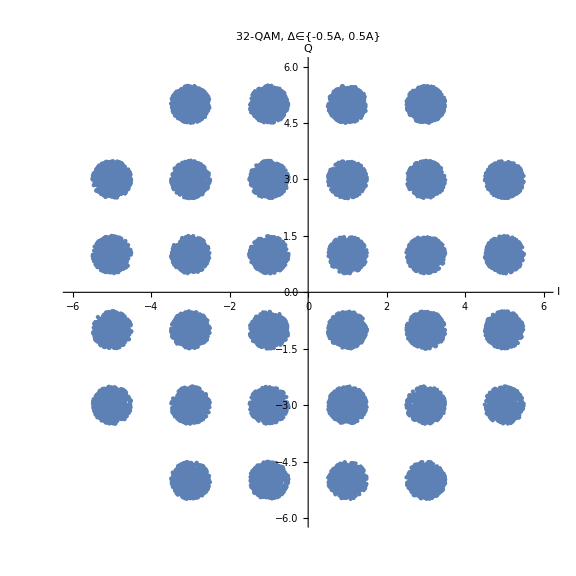

C:\Modulation\Constellation diagram\qam32n3a0.jpg

```mathematica
qam32n3a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-5,5,2},{q,-3,3,2}],1],Flatten[Table[{i,q},{i,-3,3,2},{q,-5,5,10}],1]},1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-QAM, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam32n3a0.jpg",qam32n3a0]
```

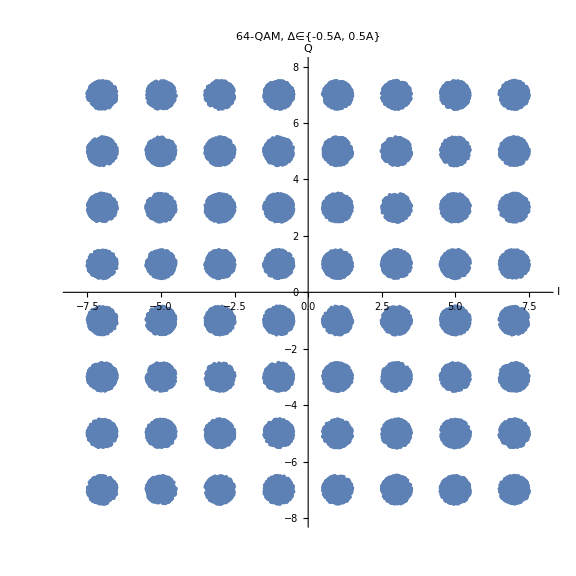

C:\Modulation\Constellation diagram\qam64n3a0.jpg

```mathematica
qam64n3a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-7,7,2},{q,-7,7,2}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-8,8},{-8,8}},AspectRatio->1,PlotLabel->Style[Framed["64-QAM, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam64n3a0.jpg",qam64n3a0]
```

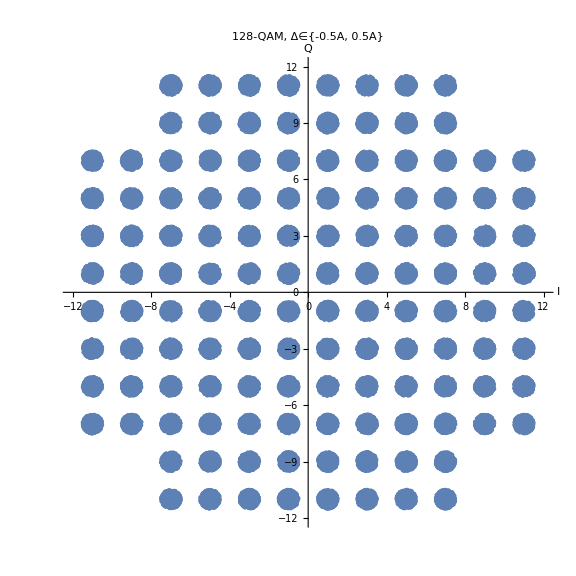

C:\Modulation\Constellation diagram\qam128n3a0.jpg

```mathematica
qam128n3a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-11,11,2},{q,-7,7,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,-11,-9,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,9,11,2}],1]},1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-12,12},{-12,12}},AspectRatio->1,PlotLabel->Style[Framed["128-QAM, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam128n3a0.jpg",qam128n3a0]
```

```mathematica
qam256n3a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-15,15,2},{q,-15,15,2}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-16,16},{-16,16}},AspectRatio->1,PlotLabel->Style[Framed["256-QAM, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam256n3a0.jpg",qam256n3a0]
```

-Graphics-

C:\Modulation\Constellation diagram\qam256n3a0.jpg

С шумом Δ∈{-1A, 1A}

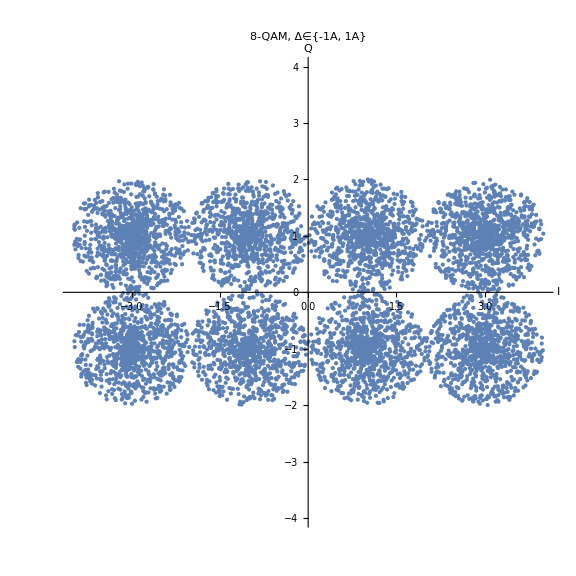

C:\Modulation\Constellation diagram\qam8n4a0.jpg

```mathematica
qam8n4a0=ListPlot[Transpose[Module[{n=8000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-1,1,2}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["8-QAM, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam8n4a0.jpg",qam8n4a0]
```

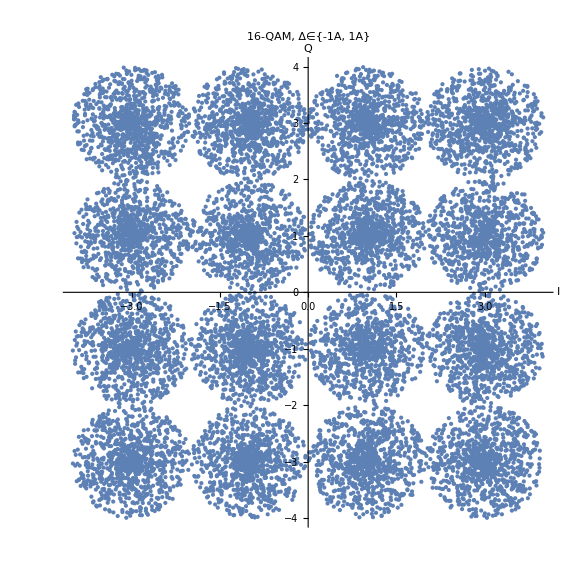

C:\Modulation\Constellation diagram\qam16n4a0.jpg

```mathematica
qam16n4a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-3,3,2},{q,-3,3,2}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-QAM, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam16n4a0.jpg",qam16n4a0]
```

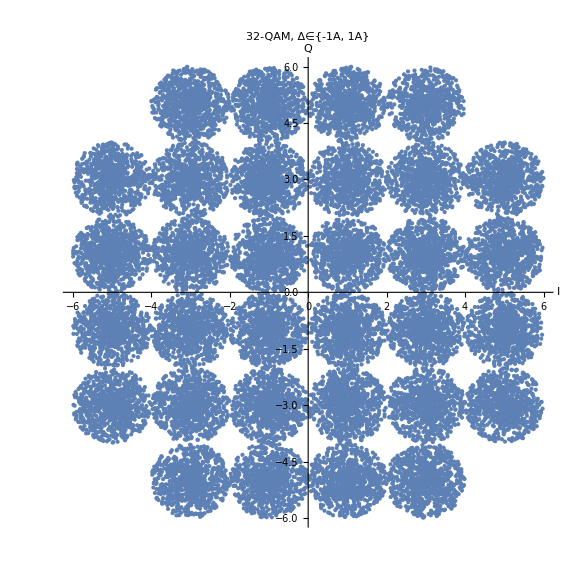

C:\Modulation\Constellation diagram\qam32n4a0.jpg

```mathematica
qam32n4a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-5,5,2},{q,-3,3,2}],1],Flatten[Table[{i,q},{i,-3,3,2},{q,-5,5,10}],1]},1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-QAM, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam32n4a0.jpg",qam32n4a0]
```

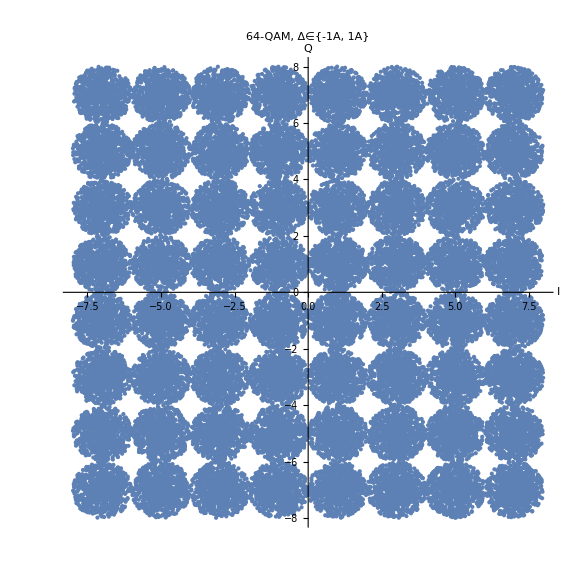

C:\Modulation\Constellation diagram\qam64n4a0.jpg

```mathematica
qam64n4a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-7,7,2},{q,-7,7,2}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-8,8},{-8,8}},AspectRatio->1,PlotLabel->Style[Framed["64-QAM, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam64n4a0.jpg",qam64n4a0]
```

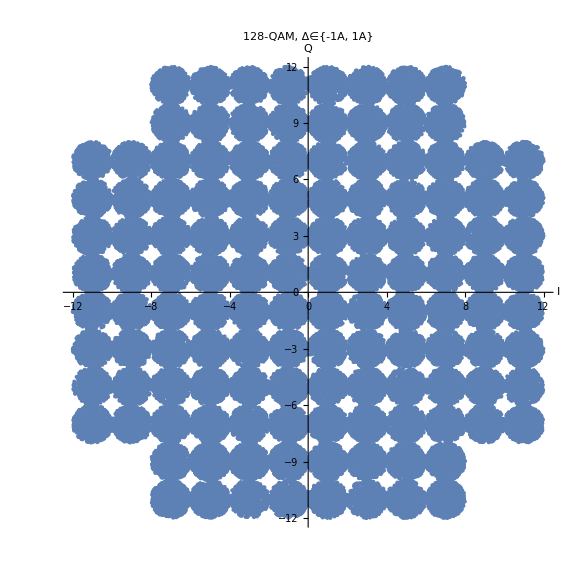

C:\Modulation\Constellation diagram\qam128n4a0.jpg

```mathematica
qam128n4a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{i,q},{i,-11,11,2},{q,-7,7,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,-11,-9,2}],1],Flatten[Table[{i,q},{i,-7,7,2},{q,9,11,2}],1]},1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-12,12},{-12,12}},AspectRatio->1,PlotLabel->Style[Framed["128-QAM, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam128n4a0.jpg",qam128n4a0]
```

```mathematica
qam256n4a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{i,q},{i,-15,15,2},{q,-15,15,2}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-16,16},{-16,16}},AspectRatio->1,PlotLabel->Style[Framed["256-QAM, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\qam256n4a0.jpg",qam256n4a0]
```

-Graphics-

C:\Modulation\Constellation diagram\qam256n4a0.jpg